# Numerisk derivering

## Exempel från föreläsningen

### Exempel 3

p2(x) = 17-11 x+2 x^2

p2'(x) = -11+4 x, => p2'(3) = 1

p2''(x) = 4, => p2''(3) = 4

Jämför med Mathematicas Fit: 17.-11. x+2. x^2

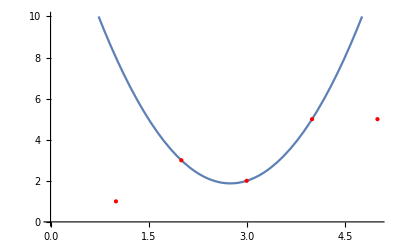

```mathematica
Remove["Global`*"]
xv={1,2,3,4,5};
fv={1,3,2,5,5};
data=Transpose[Append[{xv},fv]];
deg=2; (* 2:a-gradspolynom *)
xc=3; (* Centrering kring x-värde nr 3 i xv *)
const=Table[c[i],{i,0,deg}];
a=Transpose[Table[Table[xv[[i]]^j,{i,xc-1,xc+1}],{j,0,deg}]];
p=Table[x^i,{i,0,deg}].const;
f=Table[fv[[i]],{i,xc-1,xc+1}];
sol=Solve[a.const==f,const];
Print["p2(x) = ",pol=p/.sol[[1]]]
Print["p2'(x) = ",D[pol,x],", => p2'(",xc,") = " , D[pol,x]/.x->xc]
Print["p2''(x) = ",D[pol,{x,2}],", => p2''(",xc,") = " , D[pol,{x,2}]/.x->xc]
lp=ListPlot[data,PlotStyle->{Red,PointSize[Large]}];
pl=Plot[p/.sol[[1]],{x,0,5},PlotRange->{0,10}];
Print["Jämför med Mathematicas Fit: ",Fit[{data[[xc-1]],data[[xc]],data[[xc+1]]},{1,x,x^2},x]]
Show[pl,lp]
```